```mathematica
Clear["Global`*"]
```

### 関数

```mathematica
LoopMatrix[g_]:=(
FundLoop=FindFundamentalCycles[UndirectedGraph[g]];
RuleFundLoop=Table[EdgeRules[FundLoop[[i]]],{i,Length[FundLoop]}];
RuleRevFundLoop=Table[
EdgeRules[ReverseGraph[Graph[RuleFundLoop[[i]]]]],
{i,Length[FundLoop]}
];
Ruleg=EdgeRules[g];
Table[
Table[
If[MemberQ[RuleFundLoop[[j]],Ruleg[[i]]],1,0]+If[MemberQ[RuleRevFundLoop[[j]],Ruleg[[i]]],-1,0],
{i,EdgeCount[g]}
],
{j,Length[FundLoop]}]
)
```

```mathematica
VertexSortFromLoopEdgeList[LoopEdgeList_]:=(
UndirectedLoop=FindCycle[UndirectedGraph[LoopEdgeList]][[1]];
MinVertexNum=Min[VertexList[UndirectedLoop]];
VertexLoop={MinVertexNum};
For[j=1,Length[VertexLoop]≠ Length[UndirectedLoop],j++,
VertexLoop=Append[VertexLoop,UndirectedLoop[[FirstPosition[UndirectedLoop,VertexLoop[[j]]<->_][[1]],2]]]
];
VertexLoop=Append[VertexLoop,MinVertexNum]
)(* Vertex Sort From Loop Edge List ルールエッジで表現された巡回路から、頂点で表現された巡回路に直す *)
```

```mathematica
DelEle[list_,element_]:=list/.element->Nothing(* Delete Element *)
```

```mathematica
DelEleList[list_,elementlist_]:=list/.Table[i-> Nothing ,{i,elementlist}](* Delete Element *)
```

```mathematica
DelEdgeVertexList[edgelist_,vertexlist_]:=(
devl={};(* Variable of DelEdgeVertexList *)
Do[devl=Union[Position[edgelist,i].{{1},{0}},devl],{i,vertexlist}];
Delete[edgelist,devl]
)(* Delete Edge list from Vertex List 頂点リストから枝リストを削除（頂点リストにある頂点で構成される枝はすべて枝リストから削除）頂点リストに重複があってもUnionがあるのでOK *)
```

```mathematica
EdgeNum[Edge_]:=(
FirstPosition[EdgeRules[Gin],Edge,
FirstPosition[
EdgeRules[Gin],
EdgeRules[
ReverseGraph[{Edge}]
][[1]]
]
][[1]]
) (* Edge Number *)
```

```mathematica
EdgeNumList[Edge_]:=Table[EdgeNum[Edge[[i]]],{i,Length[Edge]}] (* Edge Number List *)
```

```mathematica
EdgeD[Edge_]:=PD[[EdgeNum[Edge]]](* Edge Distance *)
```

```mathematica
EdgeDList[Edge_]:=PD[[EdgeNumList[Edge]]](* Edge Distance *)
```

```mathematica
ListPosRef[list1_,list2_,element_]:=list1[[FirstPosition[list2,element][[1]]]](* list2でのelementの位置に来る、list1の要素を求める(list1にlist2の位置を反映 List Position Reflection) *)
```

```mathematica
EdgeReconst[Edge1_,Side1_,Edge2_,Side2_]:=VertexList[{Edge1}][[Side1]]->VertexList[{Edge2}][[Side2]](* Edge Reconstraction ２つの枝のそれぞれ片方の頂点を使って枝を再構成する *)
```

```mathematica
RestVertex[PartLoop_]:=Delete[VertexList[Gin],Table[{VertexList[PartLoop][[i]]},{i,Length[VertexList[PartLoop]]}]]
```

```mathematica
TriTourDiff[Edge_,Vertex_]:=(
EdgeD[VertexList[{Edge}][[1]]->Vertex]+EdgeD[VertexList[{Edge}][[2]]->Vertex]-EdgeD[Edge]
)(* Triangle Tour Difference *)
```

```mathematica
TriTourDiffList[PartLoop_,Vertex_]:=Table[TriTourDiff[PartLoop[[i]],Vertex],{i,Length[PartLoop]}]
```

```mathematica
MinTriTourDiffPosition[PartLoop_,Vertex_]:=(
FirstPosition[TriTourDiffList[PartLoop,Vertex],Min[TriTourDiffList[PartLoop,Vertex]]][[1]]
)
```

```mathematica
MinEdgeReconstPair[EdgePair_]:=(
ReconstEdgeD1=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]];
ReconstEdgeD2=EdgeD[EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2]]+EdgeD[EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]];
If[
ReconstEdgeD1<ReconstEdgeD2,
{ReconstEdgeD1,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],1],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],2]}},
{ReconstEdgeD2,{EdgeReconst[EdgePair[[1]],1,EdgePair[[2]],2],EdgeReconst[EdgePair[[1]],2,EdgePair[[2]],1]}}
]
)(* Minimum Edge Reconstraction Pair 枝ペアを再構成し、枝のコストが小さいほうのコストと枝ペアを出力 *)
```

```mathematica
SquareTourDiff[Edge1_,Edge2_]:=(
MinEdgeReconstPair[{Edge1,Edge2}][[1]]-EdgeD[Edge1]-EdgeD[Edge2]
)(* Square Tour Difference *)
```

```mathematica
SquareTourDiffList[PartLoop1_,PartLoop2_]:=Table[SquareTourDiff[i,j],{i,PartLoop1},{j,PartLoop2}]
```

```mathematica
MinSquareTourDiffEdgePair[PartLoop1_,PartLoop2_]:=(
PairNum=FirstPosition[SquareTourDiffList[PartLoop1,PartLoop2],Min[SquareTourDiffList[PartLoop1,PartLoop2]]];
{PartLoop1[[PairNum[[1]]]],PartLoop2[[PairNum[[2]]]]}
)(* 最小のスクエアツアとなるPartLoopの枝ペア *)
```

```mathematica
JoinPartLoop[PartLoop1_,PartLoop2_]:=Join[DelEleList[Join[PartLoop1,PartLoop2],MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop1,PartLoop2]][[2]]]
```

```mathematica
RestVertexMinCost[PartLoop_]:=Table[Min[TriTourDiffList[PartLoop,i]],{i,RestVertex[PartLoop]}](* 残りの頂点のそれぞれの追加コストが最小になる位置での追加コストのリスト *)
```

```mathematica
MinRestVertex[PartLoop_]:=RestVertex[PartLoop][[
FirstPosition[RestVertexMinCost[PartLoop],Min[RestVertexMinCost[PartLoop]]][[1]]
]](* 残りの頂点の中でも最小の追加コストとなる頂点 *)
```

```mathematica
LoopDelEdge[PartLoop_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,MinRestVertex[PartLoop]]]](* 頂点を追加するときに削除すべき枝 *)
```

```mathematica
InsertVertexLoop[PartLoop_]:=EdgeRules[EdgeAdd[EdgeDelete[PartLoop,LoopDelEdge[PartLoop]],{VertexList[{LoopDelEdge[PartLoop]}][[1]]-> MinRestVertex[PartLoop],MinRestVertex[PartLoop]-> VertexList[{LoopDelEdge[PartLoop]}][[2]]}]](* １つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
ContinuousInsertVertexLoop[PartLoop_]:=(
PartLoopSolution={PartLoop};
For[j=1,Min[RestVertexMinCost[PartLoopSolution[[-1]]]]≤1,
PartLoopSolution=Append[PartLoopSolution,InsertVertexLoop[PartLoopSolution[[-1]]]]
];
PartLoopSolution)(* 連続で１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
OutVertex[PartLoop_]:=Table[If[!RegionMember[
Polygon[Pin[[VertexSortFromLoopEdgeList[PartLoop]]]],Pin[[i]]
],i],{i,Range[Length[Pin]]}]/.Null->Nothing(* PartLoopの外側の頂点 *)
```

```mathematica
InsertDetachedEdge[PartLoop_,DetachedEdge_]:=Join[DelEleList[Append[PartLoop,DetachedEdge],{MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}][[1]]}],MinEdgeReconstPair[MinSquareTourDiffEdgePair[PartLoop,{DetachedEdge}]][[2]]](* PartLoopのどの頂点にも接していない枝を挿入 *)
```

```mathematica
EdgeLoopSide[PartLoop_,ContactEdge_]:=Intersection[VertexList[PartLoop],VertexList[{ContactEdge}]][[1]](* PartLoopに接する枝のPartLoop側の頂点 *)
```

```mathematica
EdgeRestSide[PartLoop_,ContactEdge_]:=DelEle[VertexList[{ContactEdge}],EdgeLoopSide[PartLoop,ContactEdge]][[1]](* PartLoopに接する枝のPartLoop側でない頂点 *)
```

```mathematica
DelEdgeContactEdge[PartLoop_,ContactEdge_]:=PartLoop[[MinTriTourDiffPosition[PartLoop,EdgeRestSide[PartLoop,ContactEdge]]]](* PartLoopに接する枝を挿入する際に削除すべき枝 *)
```

```mathematica
InsertContactEdge[PartLoop_,ContactEdge_]:=Join[DelEle[PartLoop,DelEdgeContactEdge[PartLoop,ContactEdge]],{ContactEdge,EdgeRestSide[PartLoop,ContactEdge]->DelEle[VertexList[{DelEdgeContactEdge[PartLoop,ContactEdge]}],EdgeLoopSide[PartLoop,ContactEdge]][[1]]}](* PartLoopの頂点に接する枝を挿入 *)
```

```mathematica
InsertEdge[PartLoop_,ContactEdge_]:=If[IntersectingQ[VertexList[PartLoop],VertexList[{ContactEdge}]],InsertContactEdge[PartLoop,ContactEdge],InsertDetachedEdge[PartLoop,ContactEdge]](* PartLoopの頂点に接する枝か否かを判定し、枝を挿入 *)
```

```mathematica
EdgeNumListVertex[VertexPairList_]:=EdgeNumList[Table[i[[1]]-> i[[2]],{i,VertexPairList}]](* Edge Num List from Vertex 枝の頂点ペアのリストから枝番号のリストを出力 *)
```

```mathematica
ComplementIntersection[List1_,List2_]:=Complement[List1∪List2,List1∩List2](* 2つのリストの共通集合の補集合を求める *)
```

```mathematica
EdgeRulesList[GraphList_]:=Table[EdgeRules[GraphList[[i]]],{i,Length[GraphList]}](* <->や->で表現されるグラフリストを枝の規則のリスト群に変換する *)
```

```mathematica
GreedyDirectedPartLoop[Rank_]:=(
DelEdge={};
EdgeProcess={};
PartLoopProcess={};
For[i=1,PartLoopProcess=={},i++,
AddEdge=EdgeRules[Gout][[Rank[[i]]]];
If[(PartLoopProcess=FindCycle[Graph[Append[EdgeProcess,AddEdge]],Infinity,All])=={},
If[FindCycle[UndirectedGraph[Append[EdgeProcess,AddEdge]],Infinity,All]=={},
EdgeProcess=Append[EdgeProcess,AddEdge],
DelEdge=Append[DelEdge,AddEdge];
]
]
];
EdgeRulesList[PartLoopProcess][[1]]
)
(* （新）Greedyを使った枝のランクを入力とした有向部分巡回路の構築(有向閉路ではないが無向閉路となるとき枝を加えない) *)
```

```mathematica
InsertVertex[PartLoop_,Vertex_]:=(
DelEdgeNum=MinTriTourDiffPosition[PartLoop,Vertex];
Join[Delete[PartLoop,DelEdgeNum],EdgeRules[Gout][[EdgeNumListVertex[{{PartLoop[[DelEdgeNum,1]],Vertex},{PartLoop[[DelEdgeNum,2]],Vertex}}]]]]
)(* 挿入したい１つの頂点を閉路に挿入したときの閉路の枝リスト *)
```

```mathematica
SortSameAs[ReferredList_,SortedList_]:=DelEleList[ReferredList,DelEleList[ReferredList,SortedList]](* 参照するリストと同じ並びでリストを並べ替える(参照するリストにない要素がある場合、その要素は出力されない) *)
```

```mathematica
OutEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Join[Subsets[OutVertex[PartLoop],{2}],Tuples[{OutVertex[PartLoop],VertexList[PartLoop]}]]]](* PartLoopの頂点を使う枝を含む、PartLoopよりも外側の枝をランク順に出力 *)
```

```mathematica
EdgeRulesLine[LineList_]:=Table[i[[1]]-> i[[2]],{i,ToExpression[StringDelete[ToString[LineList],{"Line[","]"}]]}](* Edge Rules list from Line list: Lineのリストから枝の規則のリストを出力 *)
```

```mathematica
EdgeRulesMesh[mesh_]:=EdgeRulesLine[MeshCells[mesh,1]](* Edge Rules list from Mesh: MeshRegionのリストから枝の規則を出力 *)
```

```mathematica
InVertex[PartLoop_]:=DelEleList[Range[Length[Pin]],Join[VertexList[PartLoop],OutVertex[PartLoop]]](* PartLoopの内側の頂点 *)
```

```mathematica
InEdgeRank[PartLoop_,Rank_]:=SortSameAs[Rank,EdgeNumListVertex[Subsets[InVertex[PartLoop],{2}]]](* PartLoopよりも内側の枝をランク順に出力 *)
```

### 渦電流の計算

```mathematica
Pin=Drop[Drop[Import["eil51.tsp","Table"],6],-1][[All,2;;3]](*Point input*)
```

{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}}

```mathematica
Pin=Delete[{{37,52},{49,49},{52,64},{20,26},{40,30},{21,47},{17,63},{31,62},{52,33},{51,21},{42,41},{31,32},{5,25},{12,42},{36,16},{52,41},{27,23},{17,33},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{30,48},{43,67},{58,48},{58,27},{37,69},{38,46},{46,10},{61,33},{62,63},{63,69},{32,22},{45,35},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{32,39},{25,32},{25,55},{48,28},{56,37},{30,40}},{{1},{27},{32},{2},{48},{6},{51},{46},{11},{38},{5},{49},{9},{12},{47},{18},{4},{17},{37}}]
```

{{52,64},{17,63},{31,62},{51,21},{5,25},{12,42},{36,16},{52,41},{13,13},{57,58},{62,42},{42,57},{16,57},{8,52},{7,38},{27,68},{43,67},{58,48},{58,27},{37,69},{46,10},{61,33},{62,63},{63,69},{59,15},{5,6},{10,17},{21,10},{5,64},{30,15},{39,10},{56,37}}

```mathematica
Pin=%;
```

```mathematica
Table[{i},{i,{1,27,32,2,48,6,51,46,11,38,5,49,9,12,47,18,4,17,37}}]
```

{{1},{27},{32},{2},{48},{6},{51},{46},{11},{38},{5},{49},{9},{12},{47},{18},{4},{17},{37}}

```mathematica
Gin=DirectedGraph[CompleteGraph[Length[Pin],VertexLabels->"Name",EdgeLabels->"Name"],"Acyclic"];
```

```mathematica
h=LoopMatrix[Gin];
PD=Table[
EuclideanDistance[
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[1,1]]]],
Pin[[ConnectedComponents[{EdgeRules[Gin][[i]]}][[2,1]]]]
],
{i,Length[EdgeRules[Gin]]}];(* Point Distance *)
r=IdentityMatrix[Length[EdgeRules[Gin]]]PD;
s=Table[0,{i,Length[EdgeRules[Gin]]}];
FLP=Table[
Pin[[
ConnectedComponents[RuleFundLoop[[i]]][[1]]
]],
{i,Length[RuleFundLoop]}];(* Fundamental Loop Point *)
LoopSpin=Table[
If[(Append[FLP[[i,2]]-FLP[[i,1]],0]×Append[FLP[[i,3]]-FLP[[i,2]],0]).{0,0,1}>0,1,-1],
{i,Length[RuleFundLoop]}];(* 右回りならば負、左回りならば正 *)
FLA=Table[
Area[Polygon[
Pin[[ConnectedComponents[RuleFundLoop[[i]]][[1]]]]
]],
{i,Length[RuleFundLoop]}]//N;(* Fundamental Loop Area *)
U=Table[LoopSpin[[i]]FLA[[i]],{i,Length[RuleFundLoop]}];(* 誘導起電力は右回りなら負、左回りなら正 *)
Curr=Transpose[h].Inverse[h.r.Transpose[h]//N].(h.s+U);(* 誘導起電力行列を考慮した電流を求める式 *)
```

NIntegrate::femtemnm: -- Message text not found --

```mathematica
Curr=Transpose[h].Inverse[h.r.Transpose[h]//N].(h.s+U)
```

{11.7688,10.8004,-7.35721,4.71824,6.74813,-3.61688,-7.38569,1.09381,-11.562,-11.4681,5.30035,10.0732,9.30614,6.53171,12.7808,13.5898,-10.8477,-9.27564,13.3485,-6.61117,-10.4077,-10.2909,-6.85178,-9.45858,1.53478,2.50678,-0.986349,11.9158,-2.11361,-4.85019,-8.93382,-11.3811,0.434482,13.4275,12.0897,4.67347,-4.34077,10.5891,-9.79573,-6.02541,-8.9412,10.168,14.0965,13.3657,-15.2941,-12.9306,-7.20242,-2.00247,-14.1767,2.82584,-3.77507,-10.9555,-12.4352,-0.301851,11.9143,11.7652,8.57952,10.3363,6.45287,4.47908,-3.87058,-2.05577,9.35007,9.83183,1.66765,-5.25972,6.49197,-9.50877,-7.15535,-8.24592,11.3267,11.1081,10.0063,3.98669,-10.7239,-7.86484,-4.09502,-9.14116,-0.481056,-5.49538,-10.0192,-10.7497,-3.18984,7.26807,7.68589,4.6598,10.9372,3.21498,1.07908,-5.20942,-8.36829,-5.06828,-11.7988,7.89386,-10.9785,8.98116,11.1913,4.57165,-1.68551,-3.75649,-6.33019,1.90492,5.36233,9.61115,12.6106,4.05006,-11.98,12.1305,9.87004,9.45192,2.32696,-11.3773,-9.83253,-12.0323,-2.12826,-11.2444,-12.6205,10.2666,-13.223,10.6827,1.66104,15.2588,-2.27258,2.46635,-5.19154,-13.483,-16.1869,-16.3614,-11.3057,-7.15469,0.337072,6.61148,-8.95313,11.559,4.94759,-2.52655,-3.763,9.68102,14.3639,16.4667,14.3593,-16.5287,11.9147,12.323,3.44501,8.279,-0.448081,12.171,-4.67673,-0.703924,-6.36113,-12.5373,-11.8504,8.80858,-11.3095,-8.49057,-2.31566,3.10559,-9.83784,7.4264,1.50504,-5.19039,-6.40916,5.17987,12.257,13.0762,11.1164,-11.4791,9.75087,8.58751,0.724795,6.64149,-11.8463,5.55182,8.75352,1.53729,-5.60246,-7.73069,-9.60256,-2.3765,1.3972,6.94349,11.1933,-0.112079,9.58687,10.2883,6.09879,5.45065,11.9377,-11.2493,-11.1837,-11.7864,-6.73706,-10.9367,5.01001,8.66053,-4.3408,7.73526,0.769426,6.3372,3.18049,1.94681,-0.181125,5.59708,7.09813,5.80354,-7.14378,6.56163,-8.18136,-5.19784,7.50842,7.09966,-8.08907,-4.36949,-3.20675,-5.65787,3.61987,-5.77401,-7.40796,-4.94532,1.33425,5.91227,-2.35357,-10.936,-13.5761,-14.4405,-8.14292,-3.71195,3.67329,9.68846,-5.56687,14.2013,8.22718,1.44061,0.399399,12.9356,-2.17777,-13.3437,15.3159,-13.7279,12.312,14.5909,6.38508,-12.6371,7.15085,8.14947,7.14514,4.26658,11.0327,12.0004,-11.6482,-10.7002,11.7789,-8.56745,-11.6976,2.03363,4.23078,-11.1362,-1.10312,0.0771012,-3.31856,9.73051,-4.16995,-6.8877,-9.94321,7.87349,4.45529,2.86906,-0.152349,7.92931,10.2566,10.7852,-12.2096,9.46268,-11.6852,-12.6801,13.2722,12.5968,-13.2164,-6.16,-4.53841,-7.60008,5.24041,-7.72385,-10.2835,-7.3887,8.22026,7.73231,6.20876,8.13847,1.76373,-8.12004,-6.07002,5.29681,-3.70785,-6.99631,-6.13588,-5.53978,-5.81273,2.7834,3.53944,0.687386,8.78585,-0.234104,-2.32701,-6.53522,12.4019,13.3437,-13.1999,-11.3225,-5.72226,-0.583325,-12.4394,3.98817,-2.2723,-9.05046,-10.3842,1.14624,11.9727,12.0547,9.15385,2.003,7.27431,5.49787,-2.53284,15.4631,-13.6413,-10.9116,-4.42168,1.39339,-12.2969,6.50388,-0.433131,-8.09028,-9.57514,3.60905,14.8413,14.7069,11.74,-11.8344,9.47924,7.9726,-0.999641,-11.9504,-8.54544,-1.67064,4.28112,-10.1045,9.1301,2.56456,-4.80644,-6.12036,6.78627,14.6313,15.5585,13.1329,-14.9719,11.1758,10.2808,1.55465,-13.3589,-8.69974,-4.29501,-14.4306,0.0690891,-5.94409,-12.2897,-13.6301,-3.12155,9.27215,9.41101,6.03677,14.7786,4.13282,1.82385,-5.60493,-10.3807,-7.46971,12.9864,-4.13681,-8.80891,-12.5072,-12.4735,-7.11504,4.41297,5.06746,1.62296,13.1595,0.206135,-2.37691,-7.86866,-10.7294,9.81271,-9.63206,-11.2176,10.2384,9.52306,-11.3224,-3.69779,-2.3386,-5.39334,6.67252,-5.80343,-8.2388,-9.61339,6.30868,-13.6731,12.7039,11.7681,11.4286,-11.4598,-10.1957,-8.40926,-11.0327,0.591354,-10.4994,-12.7166,9.49554,-2.51762,-7.78935,-12.9125,-13.8018,-5.64631,6.45359,6.90283,3.43568,14.4029,1.79821,-0.727558,-7.0509,13.0827,9.55121,9.09457,16.2994,-15.0802,-12.9735,-15.0886,-5.15859,-12.0102,-14.1704,10.5707,12.7609,12.3746,-13.4845,-8.66931,-6.89477,-9.73003,2.61692,-9.45871,-11.8743,5.09367,8.40598,-12.6057,-1.18475,0.0781965,-3.63383,11.2257,-4.61276,-7.65847,-10.247,-12.4176,-0.0482778,1.17573,-2.73569,13.0607,-3.87511,-7.08228,-9.75543,-14.0972,-11.5683,-14.1345,-1.6907,-12.2707,-14.975,10.2609,-5.79891,11.7635,-15.8195,10.7411,14.8398,6.56941,14.2715,-14.8622,11.9636,13.4449,5.16644,-11.4975,11.0133,15.4457,7.78367,8.68823,6.88842,-2.93535,11.6199,7.7713,9.68614}

```mathematica
Curr//N
```

{11.7688+0.000168828 (0.+Re[NDSolve`FEM`FEMNBoundaryIntegrate[1,{MeasureDump`X$30630[1],MeasureDump`X$30630[2]},Polygon[{{37.,69.},{52.,64.},{43.,67.}}]]]),10.8004+1,492,1,9.68614-0.0000178325 (0.+Re[NDSolve`FEM`FEMNBoundaryIntegrate[1,{MeasureDump`X$104385[1],20[2]},Polygon[{{37.,69.},{52.,64.},{43.,67.}}]]])}
 |  |  |  |

```mathematica
Graphics[Point[{{25,55},{37,52},{49,49}}]]
```

-Graphics-

```mathematica
Graphics[Polygon[{{25,55},{37,52},{49,49}}]]
```

-Graphics-

```mathematica
Area[Polygon[{{25,55},{37,52},{49,49}}]]
```

Area[Polygon[{{25,55},{37,52},{49,49}}]]

```mathematica
Curr
```

{11.7688+0.000168828 Area[Polygon[{{37,69},{52,64},{43,67}}]],10.8004+0.000363929 Area[Polygon[{{37,69},{52,64},{43,67}}]],492,7.7713-0.0000194922 Area[Polygon[{{37,69},{52,64},{43,67}}]],9.68614-0.0000178325 Area[Polygon[{{37,69},{52,64},{43,67}}]]}
 |  |  |  |

```mathematica
Gout=Graph[Table[If[Curr[[i]]>0,
VertexList[{EdgeRules[Gin][[i]]}][[1]]->VertexList[{EdgeRules[Gin][[i]]}][[2]],
VertexList[{EdgeRules[Gin][[i]]}][[2]]->VertexList[{EdgeRules[Gin][[i]]}][[1]]
],{i,Length[EdgeRules[Gin]]}
]];(* 電流値の正負をグラフの向きに反映した出力グラフ *)
```

### TSPの解

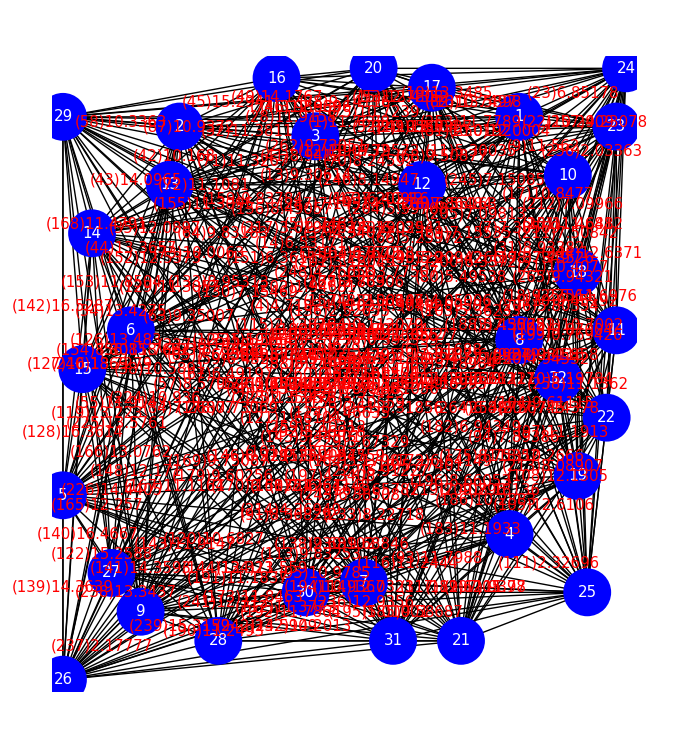

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")"<>TextString[Abs[Curr[[i]]]],FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

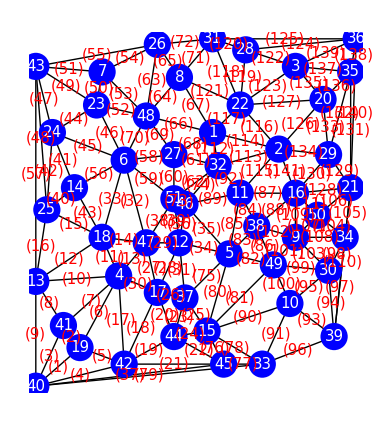

```mathematica
Graphics[{Thick,Arrowheads[{{Automatic,.8}}],Arrow[Table[
{Pin[[VertexList[{EdgeRules[Gout][[i]]}][[1]]]],Pin[[VertexList[{EdgeRules[Gout][[i]]}][[2]]]]},
{i,Length[EdgeRules[Gout]]}]],
Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}],
Red,Table[Text[Style["("<>TextString[i]<>")",FontSize->15],(Pin[[VertexList[{EdgeRules[Gin][[i]]}][[1]]]]+Pin[[VertexList[{EdgeRules[Gin][[i]]}][[2]]]])/2],
{i,Length[EdgeRules[Gin]]}]
}](* 電流値の正負をグラフの向きに反映した出力グラフの幾何学表示 *)
```

```mathematica
Grid[{EdgeRules[Gin][[1;;10]],Range[10]},Frame->All]
Grid[{EdgeRules[Gin][[11;;20]],Range[11,20]},Frame->All]
Grid[{EdgeRules[Gin][[21;;30]],Range[21,30]},Frame->All]
Grid[{EdgeRules[Gin][[31;;40]],Range[31,40]},Frame->All]
Grid[{EdgeRules[Gin][[41;;45]],Range[41,45]},Frame->All]
```

19→40 | 19→41 | 40→41 | 40→42 | 19→42 | 4→19 | 4→41 | 13→41 | 13→40 | 4→13
1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10

4→18 | 13→18 | 4→47 | 18→47 | 18→25 | 13→25 | 4→42 | 17→42 | 42→44 | 17→44
11 | 12 | 13 | 14 | 15 | 16 | 17 | 18 | 19 | 20

42→45 | 44→45 | 37→44 | 15→44 | 15→37 | 17→37 | 17→47 | 12→17 | 12→47 | 4→17
21 | 22 | 23 | 24 | 25 | 26 | 27 | 28 | 29 | 30

12→37 | 6→47 | 6→18 | 5→12 | 5→46 | 12→46 | 40→45 | 47→51 | 12→51 | 14→25
31 | 32 | 33 | 34 | 35 | 36 | 37 | 38 | 39 | 40

14→24 | 24→25 | 14→18 | 23→24 | 6→24
41 | 42 | 43 | 44 | 45

```mathematica
PDCurrCost=Abs[PD/Curr ]
```

{2.97518,1.95317,5.84619,12.9442,6.76496,13.989,3.11413,58.6966,0.675513,2.10725,2.30297,3.64078,4.90075,7.95675,1.98094,0.698084,1.57527,4.04105,1.18451,8.21826,3.10155,0.976583,1.76349,5.23308,48.6404,25.1445,63.1273,3.94435,25.4125,11.4517,3.05521,1.23324,124.371,2.96776,1.78557,10.8474,9.52368,4.7369,4.11519,8.24157,2.87544,0.598227,1.00824,2.01454,0.731023,2.03438,6.06154,27.2474,1.47288,21.3796,14.1068,4.10752,3.7305,211.299,4.88906,3.95484,6.19507,1.16498,7.70653,12.8117,12.1099,22.1902,4.83651,2.80581,27.7461,5.6464,8.04094,2.76649,5.15583,1.46534,1.39594,2.2578,3.39197,1.80879,1.21225,3.86706,10.7946,1.00858,112.503,7.5928,3.09567,3.04721,17.1508,8.49489,6.46104,11.3638,2.38423,14.6224,48.7563,6.78681,5.51768,8.73955,1.34008,2.53678,3.53717,4.17355,2.1183,8.11698,29.789,14.1114,7.45158,27.7035,8.70712,2.90211,0.731097,12.3455,1.0086,1.28771,4.39883,5.23463,4.29745,4.25266,4.18963,2.6556,29.5867,1.94233,1.28987,1.63278,1.39036,3.02171,29.8902,0.945176,27.1002,24.1171,9.42269,2.50967,1.67828,0.803903,4.27229,7.91637,171.404,8.02207,6.07674,3.77695,11.4335,27.1143,19.3465,5.67276,1.32276,0.572913,1.52735,2.35953,2.25989,3.01564,15.2083,4.2739,89.2974,2.38414,10.2122,71.0304,5.27281,1.23823,0.908858,0.726919,2.6541,4.69045,20.033,15.5796,3.74033,6.28709,33.1018,10.4484,9.00369,10.4642,2.9921,1.91798,2.99031,2.0112,3.3279,4.87555,61.0976,4.46913,1.95798,8.45802,4.20055,26.9544,8.14249,5.89948,3.79071,22.2062,36.8437,5.59272,2.19745,472.965,1.21644,2.93853,8.80703,10.9127,1.9285,2.89556,2.32653,1.37069,8.48147,0.556177,1.33896,3.34853,11.0603,2.29081,13.0615,2.97734,12.3866,23.2966,248.999,6.57427,3.87618,1.58861,2.13214,4.84099,3.85942,2.31665,3.21853,4.23728,3.32867,13.4113,15.0849,7.74861,14.4552,5.89863,4.53775,1.14388,47.1701,9.63057,22.3904,4.03276,2.89621,1.7804,6.96972,16.6419,15.5198,4.86429,10.9444,2.33332,6.32051,48.5957,187.966,3.55944,4.88122,0.374709,0.557853,3.76049,1.39029,1.79375,7.7124,1.32649,2.10231,5.0325,6.90903,12.6217,2.86627,1.3869,0.862782,2.89864,1.93782,5.74783,2.16437,3.47707,2.96162,3.86546,66.6644,808.935,18.0801,5.37947,12.1762,7.44284,2.11439,3.17521,10.8599,19.1415,361.966,5.49864,3.06152,0.66861,1.27148,3.88862,3.06175,0.714143,1.58225,2.14486,2.0555,10.9443,12.7132,6.8433,11.6591,5.42073,3.83216,1.05705,3.16292,4.44443,6.41427,2.28557,5.69808,2.26077,5.6013,2.45431,12.7216,4.37523,3.40303,4.36602,7.79497,22.637,14.4726,74.8897,4.28602,186.586,20.2387,3.73562,0.760689,1.57556,1.17852,2.54293,7.50638,88.4823,1.94437,13.9809,22.4442,5.12567,4.67128,52.4396,4.35764,3.35534,5.16343,6.50944,6.08606,9.51748,17.6566,0.907687,1.82091,3.48976,11.3441,40.1191,2.73364,8.70852,129.99,6.81175,6.01217,17.4583,3.10604,2.38371,3.74497,1.0452,4.54113,6.54762,50.3072,3.0171,5.40963,31.1084,12.1867,4.2693,5.25848,21.1463,12.5696,10.4582,8.3786,2.19136,1.36344,2.38371,1.74172,2.91049,4.13591,31.5249,1.20004,4.24056,11.9675,0.696428,883.392,8.20908,2.87684,2.64223,19.8335,7.09517,5.71232,9.65906,1.51305,12.8447,32.4744,7.57368,2.33197,5.7191,0.487013,13.7978,4.36726,1.55242,1.61139,7.6466,16.2856,11.8222,37.6462,2.89663,260.026,24.0396,4.15516,1.95724,3.02653,4.13719,1.36367,1.51627,2.26682,2.91591,18.2876,24.4335,9.83392,8.29709,7.45734,5.15673,1.163,7.44331,1.52187,0.528042,3.07793,3.70093,1.05077,5.59147,5.83055,3.69073,109.304,2.90141,2.00487,1.07398,23.706,5.55459,1.99109,1.88381,10.327,10.9491,8.48808,17.793,2.24874,30.2812,81.1398,5.27813,2.09888,5.79638,6.75132,0.854535,2.7317,2.82686,1.65688,13.1434,1.39574,0.493986,2.7238,2.35224,2.91368,1.34308,7.17118,7.75239,4.74213,24.4592,3.78983,2.68038,1.25708,0.723624,3.81523,68.04,887.843,18.4399,5.07841,12.5063,7.544,2.60401,4.36059,1773.75,63.152,26.4732,4.45726,16.3312,8.99352,3.35779,3.88339,4.23925,2.71163,43.1286,2.36335,1.37666,2.1639,2.08368,1.402,3.66635,2.47374,2.30694,9.08491,0.913598,3.18023,1.68007,2.2189,9.70877,4.89852,0.934836,1.16537,5.67908,6.33145,9.2637,19.659,0.886037,4.38264,3.294}

```mathematica
PDCurrCostSort=Ordering[PDCurrCost](* 昇順 *)
```

{238,379,440,408,194,239,140,42,272,9,364,16,276,452,154,45,105,307,128,434,251,494,326,153,482,488,122,22,43,78,107,340,411,286,418,220,405,58,489,309,19,361,75,185,32,152,451,273,108,117,139,244,195,93,444,355,395,192,474,250,241,119,439,71,477,70,49,373,396,407,141,382,17,308,277,206,383,118,437,127,484,357,23,226,35,242,74,327,422,166,189,253,116,313,2,392,173,15,421,417,168,44,46,279,476,431,245,10,265,97,207,278,475,255,354,183,485,427,72,143,292,397,290,198,11,480,210,191,377,232,442,142,473,356,338,148,87,294,479,126,94,310,460,368,155,114,450,471,441,435,331,68,64,436,249,41,367,190,225,388,252,416,104,358,443,398,186,257,34,1,200,167,165,144,344,120,393,82,31,271,275,409,81,21,337,7,287,266,483,211,496,169,213,196,320,468,73,297,256,328,95,236,12,478,414,410,53,306,159,339,240,134,449,179,453,285,209,258,76,205,469,274,28,56,224,18,52,39,359,394,391,96,113,175,212,470,362,112,348,129,146,303,111,319,461,298,381,296,495,109,288,465,172,219,341,317,156,38,447,63,208,230,170,237,55,487,13,246,457,316,69,404,321,24,110,349,151,430,262,345,284,270,91,420,412,182,293,66,138,490,291,371,378,254,432,413,3,218,178,335,47,133,323,57,160,233,491,289,85,322,342,204,433,5,90,334,282,247,227,370,445,264,406,101,403,311,459,376,80,384,59,243,216,446,299,130,14,132,67,98,177,366,20,40,402,353,174,193,425,84,103,332,92,187,467,163,481,492,125,324,37,222,372,486,401,149,423,162,352,164,77,36,267,188,280,231,424,197,329,86,135,30,283,386,363,61,263,347,106,201,458,351,248,281,295,60,374,4,199,438,214,380,314,6,51,100,217,301,88,215,145,229,158,385,466,228,83,336,325,426,261,399,456,268,137,493,369,157,305,350,50,62,180,223,315,300,202,419,390,124,400,448,26,29,464,176,123,136,48,102,65,115,99,121,428,346,360,375,161,181,387,330,472,221,234,25,89,343,318,8,171,27,463,259,454,150,302,429,312,147,415,79,33,333,131,304,235,54,203,389,269,184,260,365,455,462}

```mathematica
FindShortestTour[Pin,PerformanceGoal->"Speed"]
Graphics[Line[Pin[[Last[%]]]]]
```

{31/10+√(2/5)+(19 √2)/5+(√(13/5))/2+(√(17/5))/2+7/(√5)+(√(29/5))/2+(√(13/2))/5+3/(√10)+(√13)/5+(√(29/2))/5+(3 √17)/10+(√(41/2))/5+(√(53/2))/5+(√29)/5+(√(73/2))/5+(2 √37)/5+(3 √41)/10+(√(97/2))/5+(√58)/5+(√61)/10+(√73)/5+(√82)/5+(√89)/10+(√101)/5+(√113)/10+(√146)/5+(√173)/10,{1,32,11,38,5,37,17,4,18,47,12,46,51,27,6,48,23,7,43,24,14,25,13,41,40,19,42,44,15,45,33,39,10,49,9,30,34,21,50,16,2,29,20,35,36,3,28,31,26,8,22,1}}

-Graphics-

### 一貫した新しいgreedyを用いた解法4

```mathematica
GreedyDirectedPartLoop[PDCurrCostSort]
```

{27→9,9→28,28→30,30→31,31→21,21→4,4→19,19→22,22→11,11→18,18→10,10→1,1→17,17→20,20→16,16→2,2→13,13→14,14→15,15→5,5→27}

```mathematica
PartLoop1={27->9,9->28,28->30,30->31,31->21,21->4,4->19,19->22,22->11,11->18,18->10,10->1,1->17,17->20,20->16,16->2,2->13,13->14,14->15,15->5,5->27};
```

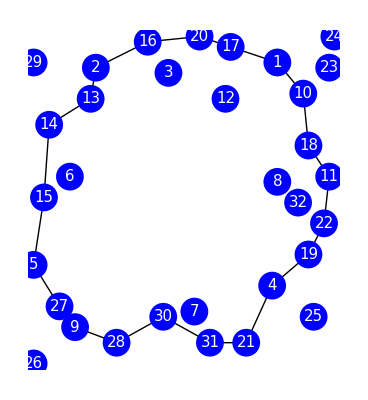

{20→3,3→22,22→2,2→20}

```mathematica
Graphics[{Table[Line[Pin[[VertexList[{i}]]]],{i,PartLoop1}],Blue,PointSize[0.05],Point[Pin],White,Table[Text[Style[i,FontSize->15],Pin[[i]]],{i,Length[Pin]}]}]
```

```mathematica
PartLoopProcess
```

{{2->16,16->29,29->20,20->2}}

{2,20,29,16,2}

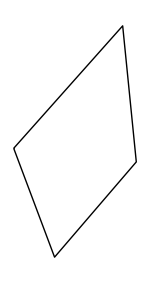

```mathematica
VertexSortFromLoopEdgeList[PartLoop1]
Graphics[line=Line[Pin[[%]]]]
```

```mathematica
MostOutEdge[PartLoop1,PDCurrCostSort]
```

114

```mathematica
OutEdgeList
```

{136,117,122,133,119,137,114,134,139,115,118,113,121,141}

```mathematica
OutEdgeRank[PartLoop1,PDCurrCostSort]
```

{101,86,82,116,105,64,114,104,128,61,115,108,98,111,106,135,67,52,99,84,46,102,23,53,63,68,25,137,136,26,118,40,58,88,127,122,54,74,131,66,130,100,70,120,121,73,24,113,85,80,119,69,126,139,138,20,117,89,50,34,76,56,75,36,2,123,59,81,8,97,77,60,41,42,35,45,103,110,124,92,38,16,96,55,5,47,93,9,72,71,14,87,65,3,39,90,12,15,33,107,13,18,22,28,109,4,21,11,43,78,51,37,49,31,95,29,7,79,62,134,83,1,44,112,6,57,10,30,27,48,32,19,91,17,94}

```mathematica
PluralPartLoopByGreedyFromRank2[OutEdgeRank[PartLoop1,PDCurrCostSort]]
```

{49→9,9→38,38→49}

```mathematica
FirstPosition[OutEdgeRank[PartLoop1,PDCurrCostSort],55]
```

{84}

```mathematica
EdgeRules[Gout][[OutEdgeRank[PartLoop1,PDCurrCostSort]]]
```

{49→9,38→49,5→49,22→1,34→21,48→8,2→11,34→50,21→29,46→51,22→2,9→34,30→34,1→32,50→21,35→20,8→1,23→48,49→30,11→38,6→23,9→38,37→44,7→48,48→26,1→27,15→37,35→36,35→3,17→37,28→22,14→25,27→6,16→38,16→21,3→22,26→7,32→27,29→35,1→48,21→35,49→10,48→6,8→22,3→28,32→46,44→15,1→2,11→5,15→5,28→31,27→48,20→22,21→36,36→3,44→17,31→22,11→46,23→7,12→5,45→15,6→14,37→5,46→12,41→19,36→28,51→6,49→15,13→41,39→34,45→33,27→51,24→14,25→24,46→5,24→6,30→9,50→16,36→31,11→32,51→47,25→13,33→39,26→43,19→42,43→24,10→39,13→40,31→26,31→8,47→18,11→16,26→8,41→40,51→12,10→15,18→13,18→25,6→18,9→50,47→4,42→17,44→45,17→12,9→16,40→42,42→45,18→4,14→18,33→15,43→7,40→45,43→23,12→37,10→30,12→47,4→41,40→33,27→46,20→3,5→38,19→40,23→24,32→2,4→19,43→13,4→13,4→17,17→47,25→43,47→6,42→44,33→10,42→4,30→39}

```mathematica
PartLoop2=InsertVertex[PartLoop1,3]
```

{2→1,5→4,4→2,1→3,3→5}

{1,2,4,5,3,1}

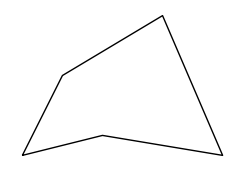

```mathematica
VertexSortFromLoopEdgeList[PartLoop2]
Graphics[line=Line[Pin[[%]]]]
```